```mathematica
Exit[]
```

## init

```mathematica
Get["/data/mapk/mapk01.mx"];
Get["/home/abergman/dicty/SPSA.m"]
```

```mathematica
LaunchKernels[]
ParallelEvaluate[$KernelID]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local],KernelObject[7,local],KernelObject[8,local],KernelObject[9,local],KernelObject[10,local],KernelObject[11,local],KernelObject[12,local],KernelObject[13,local],KernelObject[14,local],KernelObject[15,local],KernelObject[16,local]}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

```mathematica
lenX=Range[0.01,1.0,0.05]
Length[lenX]
```

{0.01,0.06,0.11,0.16,0.21,0.26,0.31,0.36,0.41,0.46,0.51,0.56,0.61,0.66,0.71,0.76,0.81,0.86,0.91,0.96}

20

```mathematica
{v,θ0}={{p1a, p1b, p1c, p1d, p2, p3a, p3b, p3c, p3d, p4, StotNative, StotOE, maxdose, dX}, {5.4, 14., 0.64, 0.013, 3.3, 0.081, 0.074, 30., 0.000025, 0.0055, 0.74, 9.6, 0.0038, 0.000063}};
inputθ0[]:=TableForm[Table[With[{i=i},InputField[Dynamic[θ0[[i]]],Number,FieldSize->{11,1}]],{i,1,Length[θ0]}],TableHeadings->{v,{"θ0"}}]
```

```mathematica
tend=10000;
slevel:={StotNative,StotOE}
pθ:=Thread[Rule[v,θ0]]
```

```mathematica
p1sigmoid=Function[s,(p1b-p1d)/(1+Exp[(p1a-Scyto[s][t])/p1c])+p1d];p3sigmoid=Function[s,p3[s]->(p3b-p3d)/(1+Exp[(Smem[s][t]-p3a)p3c])+p3d]/@{0,1};
```

```mathematica
DistributeDefinitions["Global`*"]
$DistributedContexts=None;
```

{Global`}

## Plots

### Scaffold dose response

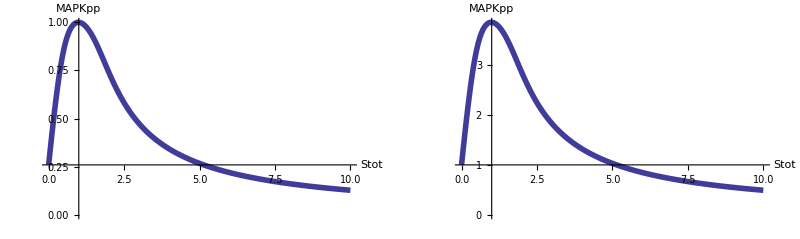

```mathematica
Block[{dat},
dat=ParallelTable[{s,MAPKpp[0]}/.runsim[p4->0,p2->0,Stot->s,p1[_]->100],{s,0.0,2.0,0.01}];
Function[ff,ListLinePlot[dat/.{s_,m_}->{s/0.2,m/ff},AxesOrigin->{1,dat[[1,-1]]/ff},AxesLabel->{"Stot","MAPKpp"},PlotStyle->Thickness[0.01],BaseStyle->{FontSize->14}]]/@{MAXMAPKPP,dat[[1,-1]]}//GraphicsRow[#,ImageSize->Full]&
]
```

### Uniform stim, no transport inhibition

```mathematica
dat=Transpose@ParallelTable[
plist=Join[{δ->maxdose*l,Stot->s,p1[a_]->p1sigmoid[a]*maxdose*l,p3[_]->p3b}/.pθ,pθ];
runsim[plist]
,{l,lenX},{s,slevel/.pθ},Method->"FinestGrained"];
Dimensions[dat]
```

{2,20,70}

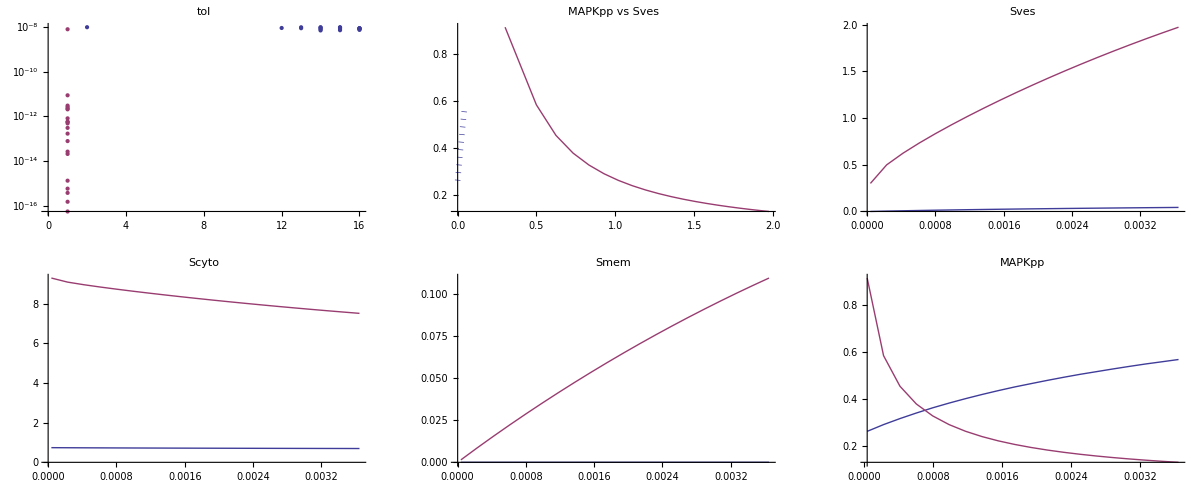

```mathematica
GraphicsGrid[{
{ListLogPlot[{runsim$maxiter,dd}/.dat,PlotLabel->"tol"],
ListLinePlot[{δ,Scyto[0]}/.dat,PlotLabel->"Scyto"]},
{
ListLinePlot[{(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0]),MAPKpp[0]/MAXMAPKPP}/.dat,PlotLabel->"MAPKpp vs Sves",PlotStyle->{{Dotted,Thickness[0.01]},Thick},PlotRange->All,AxesLabel->{}],
ListLinePlot[{δ,Smem[0]}/.dat,PlotLabel->"Smem"]
},{
ListLinePlot[{δ,(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0])}/.dat,PlotLabel->"Sves"],
ListLinePlot[{δ,MAPKpp[0]/MAXMAPKPP}/.dat,PlotLabel->"MAPKpp",PlotRange->All]
}}//Transpose,ImageSize->Full]
```

### Uniform stim, Transport Inhibition

```mathematica
dat=Transpose@ParallelTable[
plist=Join[{δ->l,Stot->s,p1[a_]->p1sigmoid[a]*l*maxdose,p3sigmoid}/.pθ,pθ];
runsim[plist]
,{l,lenX},{s,slevel/.pθ},Method->"FinestGrained"];
Dimensions[dat]
```

{2,20,71}

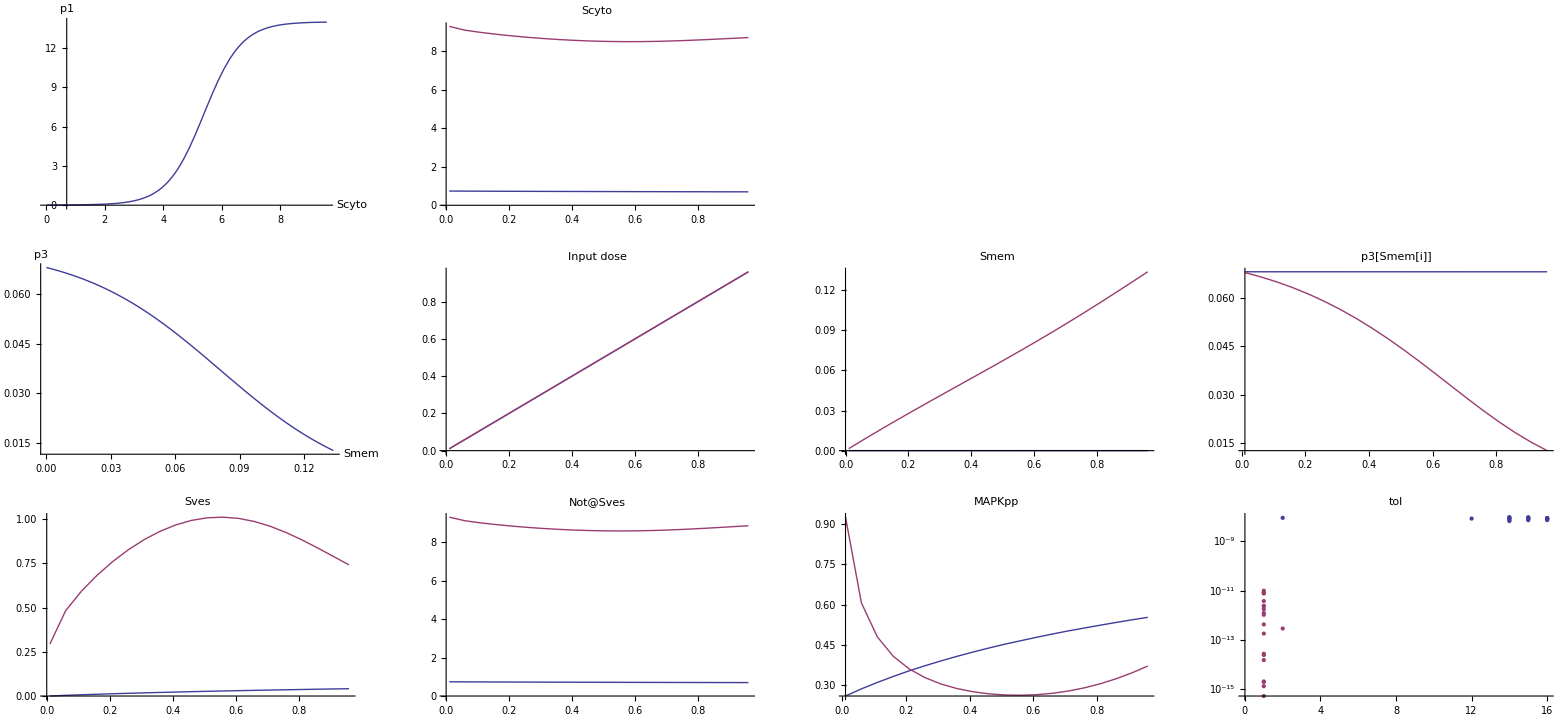

```mathematica
GraphicsGrid[{
{Plot[p1sigmoid[a]/.pθ/.Scyto[a][t]->s,{s,0,StotOE/.pθ},AxesLabel->{"Scyto","p1"},AxesOrigin->{Scyto[0]/.First[dat][[-1]],0}],
ListLinePlot[{δ,Scyto[0]}/.dat,PlotLabel->"Scyto"]
},
{Plot[p3[0]/.p3sigmoid/.pθ/.Smem[0][t]->Smem//Evaluate,{Smem,0,Max[Smem[0]/.dat]},PlotRange->{p3b/.pθ,0},AxesLabel->{"Smem","p3"}],
ListLinePlot[{δ,δ}/.dat,PlotLabel->"Input dose"],
ListLinePlot[{δ,Smem[0]}/.dat,PlotLabel->"Smem"],
ListLinePlot[{δ,p3[0]}//.(dat/.x_[t]->x),PlotLabel->"p3[Smem[i]]",PlotRange->All]},
{ListLinePlot[{δ,(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0])}/.dat,PlotLabel->"Sves"],
ListLinePlot[{δ,Stot-(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0])}/.dat,PlotLabel->"Not@Sves"],
ListLinePlot[{δ,MAPKpp[0]/MAXMAPKPP}/.dat,PlotRange->All,PlotLabel->"MAPKpp"],
ListLogPlot[{runsim$maxiter,dd}/.dat,PlotLabel->"tol"]
}
},ImageSize->Full]
```

### Gradient stim

{2,20,73}

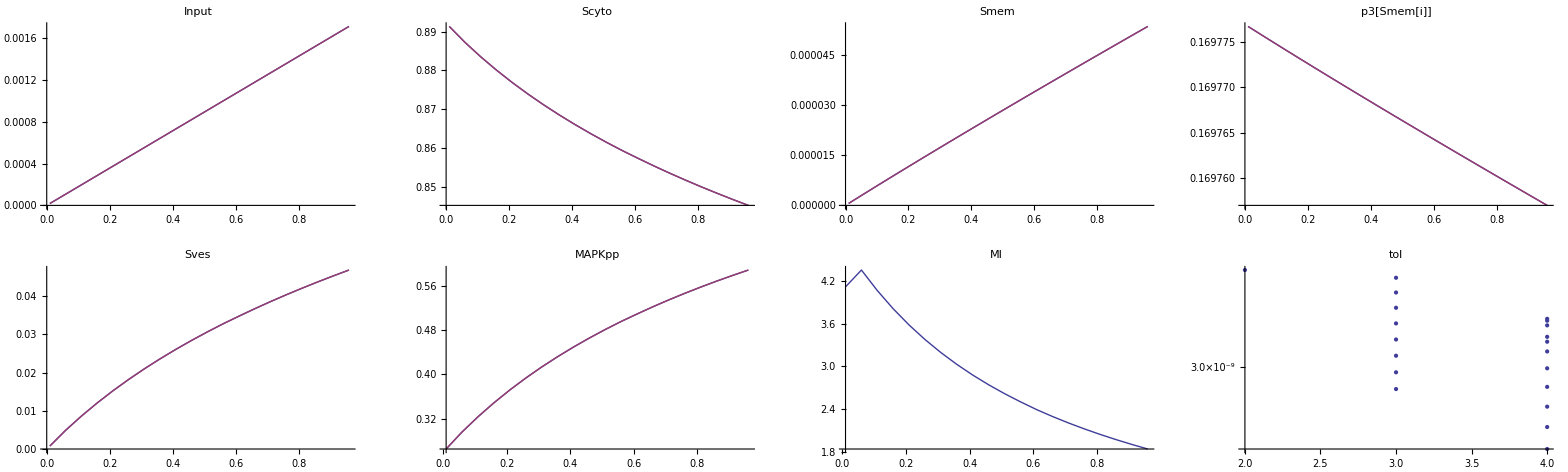

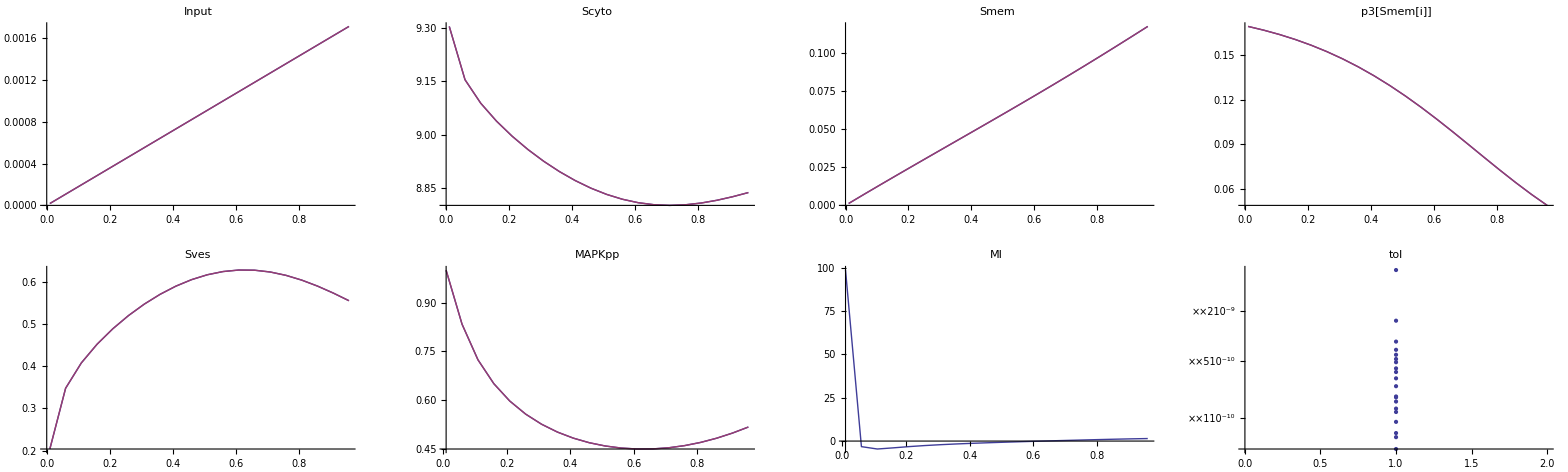

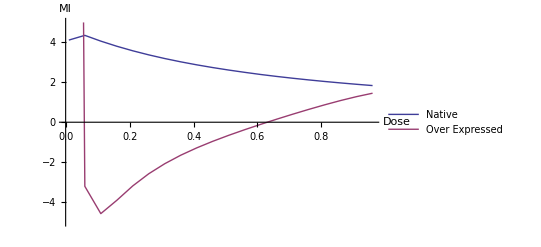

```mathematica
dat=Transpose@ParallelTable[
plist=Join[{λ->l,δ[x_]->maxdose(l+dX*x),Stot->s,p1[x_]->p1sigmoid[x]*δ[x],p3sigmoid,Di->0.0001}/.pθ,pθ];
runsim[plist]
,{l,lenX},{s,slevel/.pθ},Method->"FinestGrained"];
Dimensions[dat]
gf=Function[dat,
GraphicsGrid[{{
ListLinePlot[{{λ,δ[0]},{λ,δ[1]}}/.dat//Transpose,PlotLabel->"Input"],
ListLinePlot[{{λ,Scyto[0]},{λ,Scyto[1]}}/.dat//Transpose,PlotLabel->"Scyto"],
ListLinePlot[{{λ,Smem[0]},{λ,Smem[1]}}/.dat//Transpose,PlotLabel->"Smem"],
ListLinePlot[{{λ,p3[0]},{λ,p3[1]}}//.dat/.x_[t]->x//Transpose,PlotLabel->"p3[Smem[i]]"]
},{
ListLinePlot[{
{λ,(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0])},
{λ,(C1[1]+C2[1]+C3[1]+C4[1]+C5[1]+C6[1]+C7[1]+C8[1]+C9[1])}
}/.dat//Transpose,PlotLabel->"Sves"],
ListLinePlot[{{λ,MAPKpp[0]/MAXMAPKPP},{λ,MAPKpp[1]/MAXMAPKPP}}/.dat//Transpose,PlotRange->All,PlotLabel->"MAPKpp"],
ListLinePlot[{λ,(MAPKpp[1]-MAPKpp[0])/(dX*maxdose)}/.dat,PlotRange->All,PlotLabel->"MI"],
ListLogPlot[{runsim$maxiter,dd}/.dat,PlotLabel->"tol"]
}},ImageSize->Full]];
gf[dat[[1]]]
gf[dat[[2]]]
ListLinePlot[{λ,(MAPKpp[1]-MAPKpp[0])/(dX*maxdose)}/.dat,PlotRange->5{-1,1}10^0,AxesLabel->{"Dose","MI"},PlotLegends->LineLegend[{"Native","Over Expressed"}]]
```

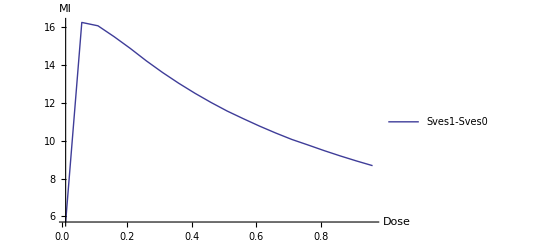

```mathematica
ListLinePlot[{λ,1/(dX*maxdose)((C1[1]+C2[1]+C3[1]+C4[1]+C5[1]+C6[1]+C7[1]+C8[1]+C9[1])-(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0]))}/.dat[[1]],PlotRange->All,AxesLabel->{"Dose","MI"},PlotLegends->LineLegend[{"Sves1-Sves0","Over Expressed"}]]
```

### MI-MAPK vs Stot

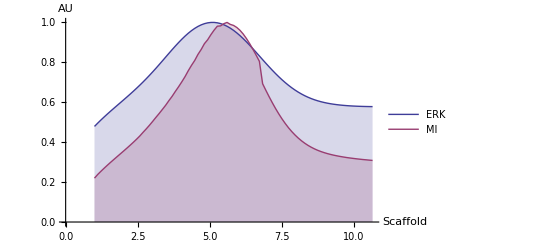

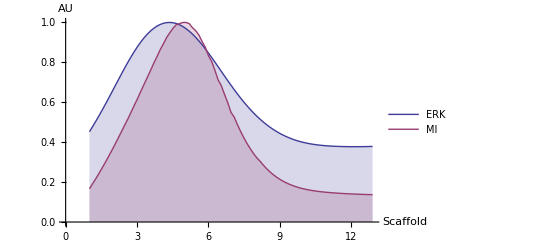

```mathematica
Block[{MI,ERK,dat},
dat=Transpose@ParallelTable[
plist=Join[{δ->l,Stot->s,p1[x_]->p1sigmoid[x]*maxdose(l+dX*x),p3sigmoid,Di->0.0001}/.pθ,pθ];
runsim[plist]
,{l,lenX},Evaluate@Flatten[{s,slevel/.pθ,.1}],Method->"FinestGrained",DistributedContexts->None];
ERK={Stot/StotNative,(MAPKpp[0]+MAPKpp[1])/(2*MAXMAPKPP)}/.dat//Transpose//Mean;
MI={Stot/StotNative,(MAPKpp[1]-MAPKpp[0])/(dX*maxdose)}/.dat//Transpose//Mean;
ListPlot[{ERKᵀ/{1,Max[ERK[[All,2]]]}//Transpose,MIᵀ/{1,Max[MI[[All,2]]]}//Transpose},Joined->True,PlotRange->{0,1},Filling->Axis,AxesLabel->{"Scaffold","AU"},PlotStyle->Thick,PlotLegends->LineLegend[{"ERK","MI"}]
]
]
```

### MI vs grad

```mathematica
grad=Range[0,1.0,0.25]//Chop
Length[grad]
DistributeDefinitions[grad];
```

{0,0.25,0.5,0.75,1.}

5

```mathematica
With[{pr={-5,20},slevel={StotNative,4*StotNative}/.pθ},
dat=ParallelTable[
plist={γ->g,λ->l,δ[x_]->g*maxdose(l+dX*x),Stot->s,p1[x_]->p1sigmoid[x]*δ[x],p3sigmoid,Di->0.0001}/.pθ//Flatten;
plist=Join[plist,pθ];
runsim[plist]
,{l,lenX},{s,slevel},{g,grad},Method->"FinestGrained",DistributedContexts:>None];

MI=If[γ==0,0,(MAPKpp[1]-MAPKpp[0])/(γ*maxdose*dX)]/.dat//Transpose;

GraphicsGrid[{
Function[{i,lbl},
ListLinePlot[{λ,MAPKpp[0]/MAXMAPKPP}/.dat[[All,i,All]]//Transpose,PlotLabel->lbl,PlotRange->{0,1},AxesLabel->{"dose","MAPKpp"},PlotStyle->({Thickness[0.01],Hue[0.7,#,1]}&/@grad)]]~MapThread~{{1,2},{"Native","Optimal"}},
Function[{mi,lbl},
ListLinePlot[{lenX,#}ᵀ&/@Transpose@mi,PlotRange->pr,PlotLabel->lbl,AxesLabel->{"dose","MI"},
PlotStyle->({Thickness[0.01],Hue[1,#,1]}&/@grad)]
]~MapThread~{MI,{"Native","Optimal"}}
,
{ListLinePlot[Map[{grad,#}ᵀ&,Mean/@MI],PlotMarkers->Automatic,PlotLegends->LineLegend[{"Native","Optimal"}],AxesLabel->{"Gradient","MI"},PlotRange->All,ImageSize->Full],SpanFromLeft}
}]]
```

-Graphics-

```mathematica
Dimensions[dat]
```

{20,2,5,74}

## Opt

### Loss

```mathematica
Loss[θ_?(VectorQ[#,NumericQ]&)]:=With[{pθ=Thread[v->Abs@θ]},
dat=Transpose@ParallelTable[
plist=Join[{λ->l,δ[x_]->maxdose(l+dX*x),Stot->s,p1[x_]->p1sigmoid[x]*δ[x],p3sigmoid,Di->0.0001}/.pθ,pθ];
runsim[plist]
,{l,lenX},{s,slevel/.pθ},Method->"FinestGrained",DistributedContexts->None];

SvesNative=(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0])/.First[dat];

MAPKppNative=(MAPKpp[0]+MAPKpp[1])/(2*MAXMAPKPP)/.First@dat;
MAPKppOE=(MAPKpp[0]+MAPKpp[1])/(2*MAXMAPKPP)/.Last@dat;
{MIsimNative,MIsimOE}={λ,(MAPKpp[1]-MAPKpp[0])/(dX*maxdose)}/.dat;

equNative=Fit[MIsimNative,{1,x},x];
MIerrorNative=Mean@Abs[MIsimNative[[All,2]]-(equNative/.x->lenX)];

MIsimOE=Select[MIsimOE,#[[1]]>0.1&];
equOE=Fit[MIsimOE,{1,x},x];
MIerrorOE=Mean@Abs[MIsimOE[[All,2]]-(equOE/.x->MIsimOE[[All,1]])];

lossfuncs=Hold[
StotNative^2/.pθ,
(StotOE/StotNative-9)^2/.pθ,
(Mean[MAPKppNative]-2.0*Mean[MAPKppOE])^2,
Mean[SvesNative]^2,
MIerrorNative,
MIerrorOE,
equNative/.a_+b_*x->(a-2)^2,
equNative/.a_+b_*x->b^2,
(x-0.8)^2/.Solve[equNative==equOE][[1]],
(x-0.2)^2/.Solve[equOE==0][[1]]
];
lossfuncsexp=List@@Map[Defer,lossfuncs];
lossfuncsval={ReleaseHold[lossfuncs]};

w.lossfuncsval
]
Loss[θ0]
```

w.{0.812104,2.01624,0.278201,0.0009749,0.182145,0.354369,5.56899,9.38604,0.0176672,0.241499}

```mathematica
w=1/lossfuncsval
```

{1.23137,0.495972,3.59452,1025.75,5.49015,2.82192,0.179566,0.106541,56.6021,4.14081}

### FD

```mathematica
δp=0.01;
grad=FDGradientP[Loss,θ0,δp]
```

{3.98361,-1.90379,-21.5441,-420.035,25.7152,-2222.65,-1029.99,-1.07502,-3608.53,6438.14,-80.6473,-5.10357,-56556.5,1074.26}

```mathematica
Loss[θ0]//ScientificForm
```

1.48101×10^2

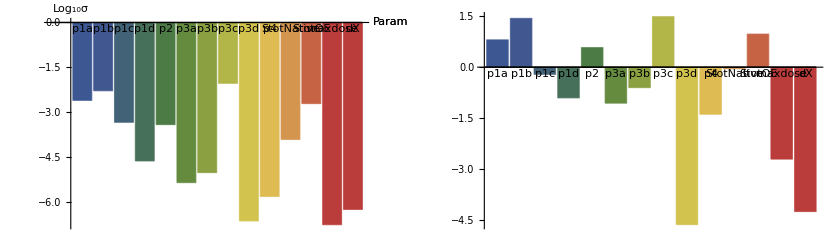

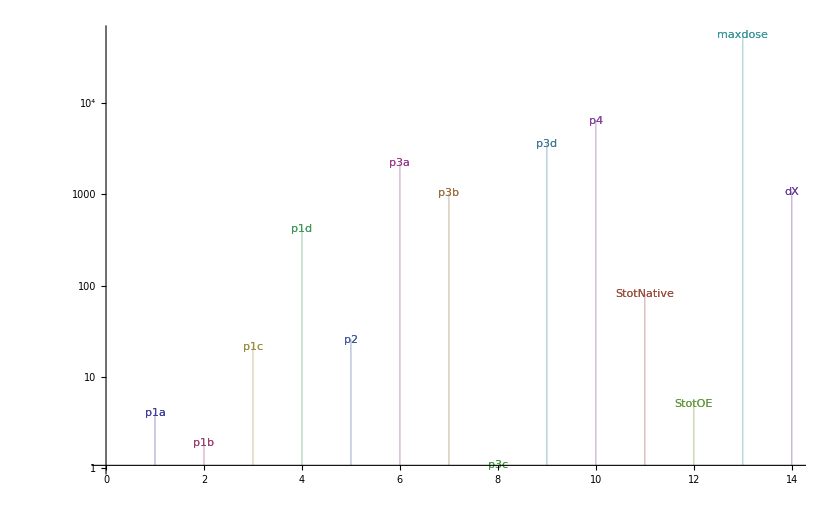

```mathematica
δL=10^-2;
σ0=δL/Abs@grad;
σ0=σ0/.ComplexInfinity->100;
σ0=MapThread[Function[{p,s},Clip[s,{0.,δp*p}]],{θ0,σ0}];
GraphicsRow[{
BarChart[Log[10,σ0],ChartLabels->v,ChartStyle->"DarkRainbow",AxesLabel->{"Param","Log_10σ"}],
BarChart[Log[10,θ0],ChartLabels->v,ChartStyle->"DarkRainbow"]}]
ListLogPlot[{Array[{#,Abs@grad[[#]]}&,Length[grad]]}ᵀ,PlotRange->All,Filling->Bottom,PlotMarkers->v]
```

```mathematica
TableForm[{θ0,δp θ0,σ0,grad}//SetPrecision[#,2]&,TableHeadings->{{"θ0","δp.θ0","σ0","grad"},v}]
```

| p1a | p1b | p1c | p1d | p2 | p3a | p3b | p3c | p3d | p4 | StotNative | StotOE | maxdose | dX
θ0 | 6.4 | 27. | 0.61 | 0.13 | 3.8 | 0.087 | 0.25 | 30. | 0.000024 | 0.041 | 0.9 | 9.4 | 0.002 | 0.000057
δp.θ0 | 0.064 | 0.27 | 0.0061 | 0.0013 | 0.038 | 0.00087 | 0.0025 | 0.3 | 2.4×10^-7 | 0.00041 | 0.009 | 0.094 | 0.00002 | 5.7×10^-7
σ0 | 0.0025 | 0.0053 | 0.00046 | 0.000024 | 0.00039 | 4.5×10^-6 | 9.7×10^-6 | 0.0093 | 2.4×10^-7 | 1.6×10^-6 | 0.00012 | 0.002 | 1.8×10^-7 | 5.7×10^-7
grad | 4. | -1.9 | -22. | -420. | 26. | -2200. | -1000. | -1.1 | -3600. | 6400. | -81. | -5.1 | -57000. | 1100.

### Viz

```mathematica
viz:=Dynamic[
GraphicsGrid[{
{ListLogPlot[{runsim$maxiter,dd}/.dat],ListLinePlot[{λ,Scyto[0]}/.dat,PlotLabel->"Scyto"],Plot[p1sigmoid[a]/.dat[[1,1]]/.Scyto[a][t]->s,{s,0,StotOE/.dat[[1,1]]},AxesLabel->{"Scyto","p1"},AxesOrigin->{Scyto[0]/.First[dat][[-1]],0}]},
{ListLinePlot[{(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0]),MAPKpp[0]/MAXMAPKPP}/.dat,PlotLabel->"MAPKpp vs Sves",PlotStyle->{{Dotted,Thickness[0.01]},Thick},PlotRange->All,AxesLabel->{}],
ListLinePlot[{λ,Smem[0]}/.dat,PlotLabel->"Smem"],
Plot[p3[0]/.p3sigmoid/.Smem[0][t]->Smem/.dat[[1,1]]//Evaluate,{Smem,0,Max[Smem[0]/.dat]},PlotRange->{p3b/.dat[[1,1]],0},AxesLabel->{"Smem","p3"}]
},{
ListLinePlot[{λ,(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0])}/.dat,PlotLabel->"Sves"],
ListLinePlot[{λ,MAPKpp[0]/MAXMAPKPP}/.dat,PlotLabel->"MAPKpp",PlotRange->All],
Show[ListPlot[{λ,(MAPKpp[1]-MAPKpp[0])/(dX*maxdose)}/.dat,PlotRange->5*10^0{-1,1},AxesLabel->{"Dose","MI"}],
Plot[{equNative,equOE},{x,0,1}]
]
}},ImageSize->Full]
,TrackedSymbols:>{dat}]
```

```mathematica
vizLossInput:=Table[With[{i=i},
{i,
InputField[Dynamic[w[[i]]],Number,FieldSize->{12,1}],
Dynamic[ScientificForm@SetPrecision[lossfuncsval[[i]],3]],
Dynamic[lossfuncsval[[i]]w[[i]]],
lossfuncsexp[[i]]
}],{i,1,Length[w]}]//TableForm[#,TableHeadings->{None,{"i","w","val","w.v","exp"}}]&
vizLossBar:=Dynamic[BarChart[w lossfuncsval//Reverse,BarOrigin->Left,ChartLabels->Reverse@lossfuncsexp,PlotRange->{{-0.51,2},All},AspectRatio->0.3,ImageSize->Full]]
```

### Run

```mathematica
vizLossInput
```

i | w | val | w.v | exp
1 |  |  |  | StotNative^2/.{p1a→6.35064,p1b→27.0871,p1c→0.614988,p1d→0.125039,p2→3.75759,p3a→0.0874926,p3b→0.250524,p3c→30.4916,p3d→0.0000236289,p4→0.0412863,StotNative→0.901168,StotOE→9.39012,maxdose→0.00198508,dX→0.0000571617}
2 |  |  |  | (StotOE/StotNative-9)^2/.{p1a→6.35064,p1b→27.0871,p1c→0.614988,p1d→0.125039,p2→3.75759,p3a→0.0874926,p3b→0.250524,p3c→30.4916,p3d→0.0000236289,p4→0.0412863,StotNative→0.901168,StotOE→9.39012,maxdose→0.00198508,dX→0.0000571617}
3 |  |  |  | (Mean[MAPKppNative]-2. Mean[MAPKppOE])^2
4 |  |  |  | Mean[SvesNative]^2
5 |  |  |  | MIerrorNative
6 |  |  |  | MIerrorOE
7 |  |  |  | equNative/.a_+b_ x→(a-2)^2
8 |  |  |  | equNative/.a_+b_ x→b^2
9 |  |  |  | (x-0.8)^2/.Solve[equNative==equOE]⟦1⟧
10 |  |  |  | (x-0.2)^2/.Solve[equOE==0]⟦1⟧

```mathematica
σmask=If[#>0,1,0]&/@SPSA`Private`σk
```

```mathematica
σmask={1,0,1,0,0,1,1,0,0,1,0}
```

{1,0,1,0,0,1,1,0,0,1,0}

```mathematica
σmask=UnitStep@σ0
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
σ0={0.001,0.001,0.0001,0.00001,0.001,0.00001,0.0001,0.01,1.*^-7,0.00001,0.001,0.001,1.*^-6,1.*^-7}
```

{0.001,0.001,0.0001,0.00001,0.001,0.00001,0.0001,0.01,1.×10^-7,0.00001,0.001,0.001,1.×10^-6,1.×10^-7}

```mathematica
SPSAMaxEvals[1000]
RandomSearchInit[Loss,ToString/@v,θ0,Chop[σ0*σmask]]
```

Start | Stop | Update | 
 | θk | σk
p1a |  | 
p1b |  | 
p1c |  | 
p1d |  | 
p2 |  | 
p3a |  | 
p3b |  | 
p3c |  | 
p3d |  | 
p4 |  | 
StotNative |  | 
StotOE |  | 
maxdose |  | 
dX |  |  |  |  |

```mathematica
θ0=Lhist[[-1,2]]
DistributeDefinitions[θ0]
```

{6.35609,27.0929,0.615554,0.125124,3.75467,0.0875588,0.251981,30.5051,0.0000248226,0.0411714,0.916318,9.39909,0.00199585,0.0000574941}

{θ0}

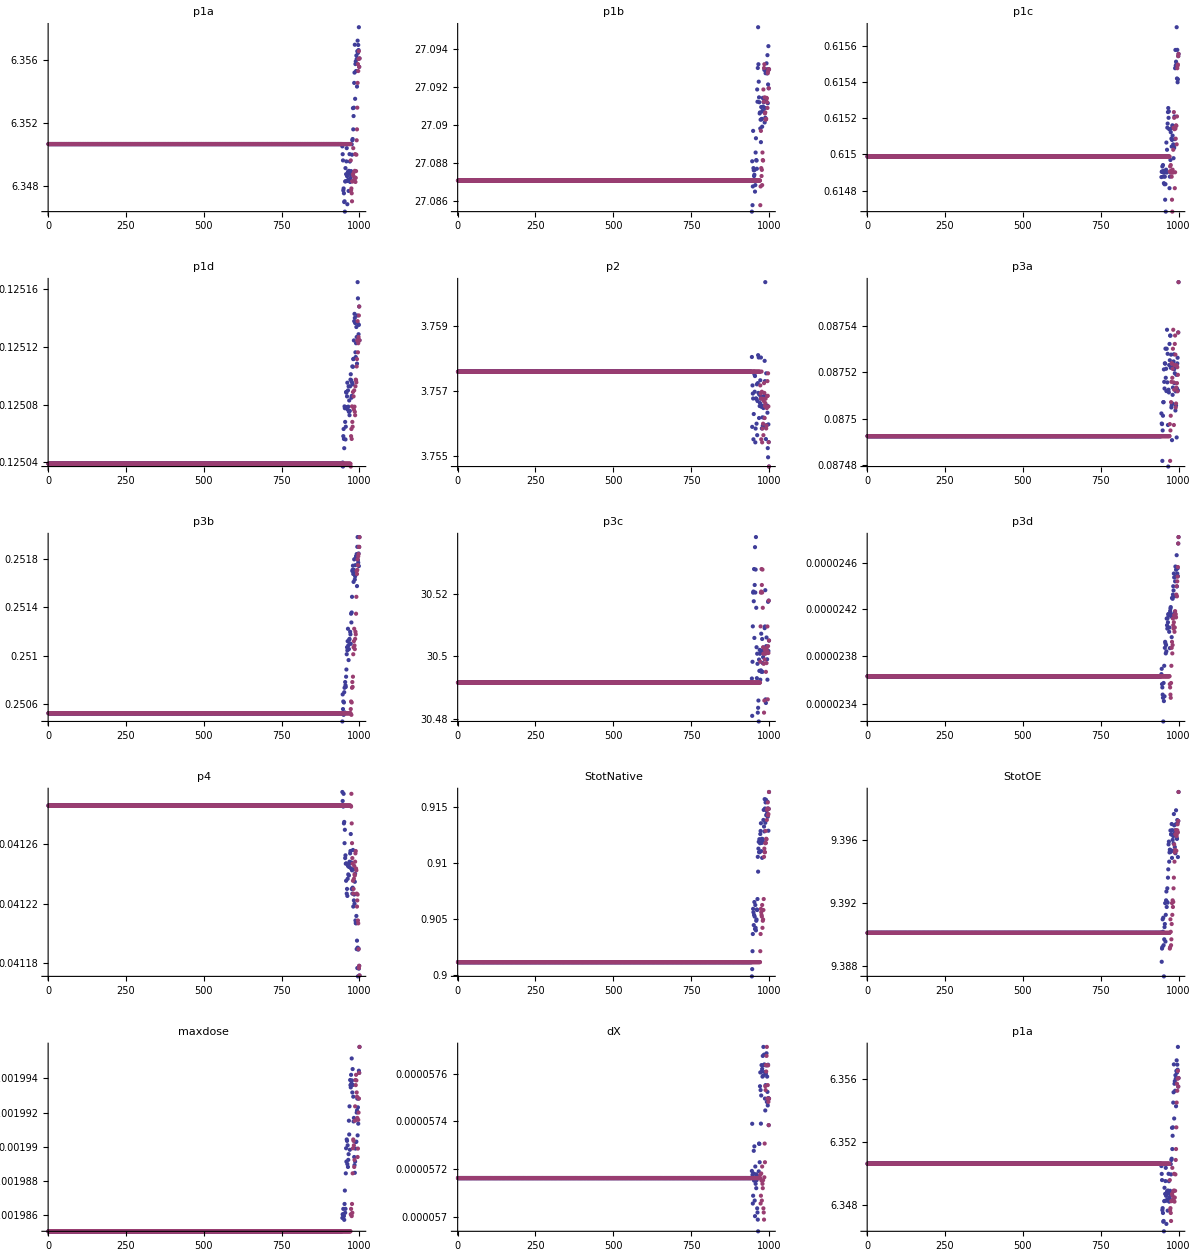

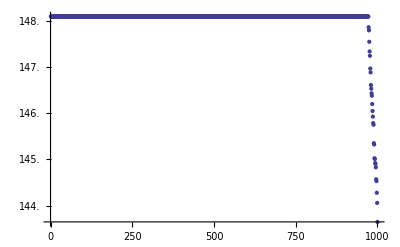

```mathematica
{sol,Lhist}=SPSAGetHistory[];
GraphicsGrid[MapThread[Function[{v,p,p2},ListLogPlot[{p,p2},PlotLabel->ToString[v],PlotRange->All]],{v,sol[[All,2]]ᵀ,Lhist[[All,2]]ᵀ}]//Partition[#,3,3,1]&,ImageSize->Full]
ListLogPlot[Lhist[[All,1]],PlotRange->All]
```